```mathematica
a=1;
α=0.3;
P1[x_,y_]:=(1-Abs[x y]/a^2)ⅇ^-α;
P2[x_,y_]:=(1-Abs[x]/a)ⅇ^(-α Abs[y]/a);
P3[x_,y_]:=(1-Abs[y]/a)ⅇ^(-α Abs[x]/a);
P4[x_,y_]:=0;
pw=Piecewise[{{P1[x,y],Abs[x]≤1&&Abs[y]≤1},{P2[x,y],Abs[x]≤1&&Abs[y]>1},{P3[x,y],Abs[x]>1&&Abs[y]≤1}},P4[x,y]]
```

Piecewise[{{0.740818 (1-Abs[x y]), Abs[x]≤1&&Abs[y]≤1}, {ⅇ^(-0.3 Abs[y]) (1-Abs[x]), Abs[x]≤1&&Abs[y]>1}, {ⅇ^(-0.3 Abs[x]) (1-Abs[y]), Abs[x]>1&&Abs[y]≤1}, {0, True}}]

```mathematica
Plot3D[pw,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

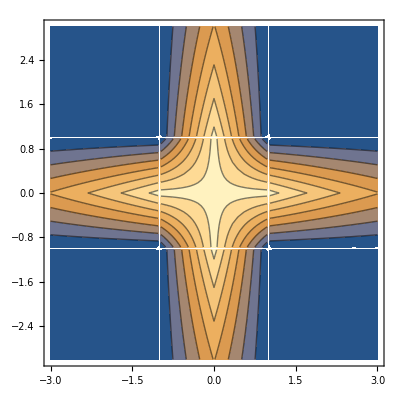

```mathematica
ContourPlot[pw,{x,-3,3},{y,-3,3}]
```